```mathematica
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];
```

## kinase competition

### combine

```mathematica
(*find the transition point: first activating E0*)
getTransitionPt[inputPoints_]:=Module[{thisTally,annihilationPts,multiSS,i,thisPoint},

thisTally=inputPoints[[;;,1]]//Tally;
annihilationPts={};

multiSS=False;
For[i=1,i<=Length[thisTally],i++,

thisPoint=thisTally[[i]];
If[thisPoint[[2]]>1,multiSS=True];
If[multiSS==True&&thisPoint[[2]]==1,AppendTo[annihilationPts,thisPoint[[1]]];multiSS=False];

];
multiSS=False;
annihilationPts[[1]]
];
```

```mathematica
decayList={1,2,3};
```

```mathematica
noDecayList={1,2,3,4,5,6};
```

```mathematica
(*construct decay list plot*)
```

```mathematica
decayPoints={};
For[i=1,i<=Length[decayList],i++,

thisData=Import["zar1Points_decay_nk_"<>ToString[decayList[[i]]]<>".mx"];
thisTransition=getTransitionPt[thisData];
AppendTo[decayPoints,{decayList[[i]],thisTransition}]

]
```

Part::partw: Part 1 of {} does not exist.

```mathematica
noDecayPoints={};
For[i=1,i<=Length[noDecayList],i++,

thisData=Import["zar1Points_noDecay_nk_"<>ToString[noDecayList[[i]]]<>".mx"];
thisTransition=getTransitionPt[thisData];
AppendTo[noDecayPoints,{noDecayList[[i]],thisTransition}]

]
```

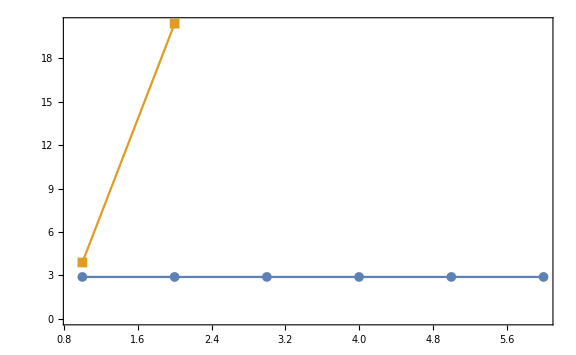

```mathematica
ListPlot[{noDecayPoints,decayPoints},PlotRange->Full,Frame->{True,True,False,False},LabelStyle->Directive[Black,20],Joined->True,PlotMarkers->{Automatic, Medium}]
```

```mathematica
(*Export["kinaseInterference.png",%,ImageResolution->200];*)
```

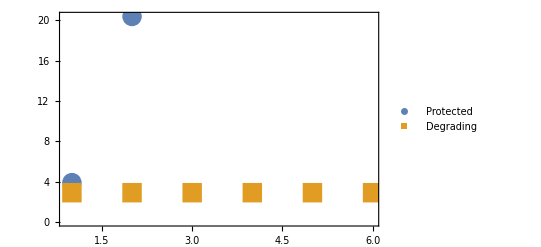

```mathematica
ListPlot[{decayPoints,noDecayPoints},PlotRange->Full,Frame->{True,True,False,False},LabelStyle->Directive[Black,15],PlotLegends->{" n+k_1⇌C","Degrading"},PlotMarkers->{Automatic,Large}]
```

```mathematica
(*Export["kinaseInterference_legend.png",%,ImageResolution->200];*)
```